```mathematica
$Assumptions= g∈Reals && τ ∈Reals && q ∈Reals&&k∈Reals
ClearAll["Global`*"]
u[q_]:= Exp[-I 3 Pi / 4] B[q] * Sqrt[τ] * Exp[-Pi * B[q]*B[q]*τ/4]* f[I*B[q]*B[q]*τ-1, Exp[I * 3* Pi/4]*2*(1-A[q])*Sqrt[τ]
]
```

g∈ℝ&&τ∈ℝ&&q∈ℝ&&k∈ℝ

```mathematica
v[q_]:=- Exp[-Pi * B[q]*B[q]*τ/4]* f[I*B[q]*B[q]*τ, Exp[I * 3* Pi/4]*2*(1-A[q])*Sqrt[τ]
]
```

```mathematica
f[a_,b_] := ParabolicCylinderD[a,b];
B[q_] := Sin[q]
A[q_] := 1+Cos[q]
ω[q_] := 2*Sqrt[(1-A[q])^2+B[q]^2]
U[q_,t_]:={{Cos[2 t]-I Cos[q] Sin[2 t],Sin[q] Sin[2 t]},{-Sin[q] Sin[2 t],Cos[2 t]+I Cos[q] Sin[2 t]}}
v[q_]:=- Exp[-Pi * B[q]*B[q]*τ/4]* f[I*B[q]*B[q]*τ, Exp[I * 3* Pi/4]*2*(1-A[q])*Sqrt[τ]
]
u[q_]:= Exp[-I 3 Pi / 4] B[q] * Sqrt[τ] * Exp[-Pi * B[q]*B[q]*τ/4]* f[I*B[q]*B[q]*τ-1, Exp[I * 3* Pi/4]*2*(1-A[q])*Sqrt[τ]
]
```

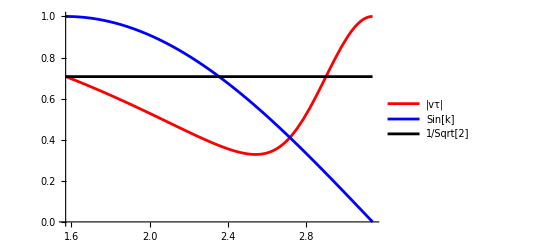

```mathematica
Plot[Evaluate[{Abs[v[k]],Sin[k],1/Sqrt[2]}/. τ->2],{k,Pi/2,Pi},PlotStyle->{Red,Blue,Black,Darker[Green]},PlotLegends->{"|vτ|","Sin[k]","1/Sqrt[2]"}]
```

```mathematica
pk = Abs[(-I*Conjugate[u[k]]*Cos[k/2]+Conjugate[v[k]]*Sin[k/2])]^2
```

Abs[-ⅈ ⅇ^((3 ⅈ π)/4-1/4 π Conjugate[τ] Conjugate[B[k]]^2) Conjugate[√τ B[k] f[-1+ⅈ τ B[k]^2,2 ⅇ^((3 ⅈ π)/4) √τ (1-A[k])]] Cos[k/2]-ⅇ^(-1/4 π Conjugate[τ] Conjugate[B[k]]^2) Conjugate[f[ⅈ τ B[k]^2,2 ⅇ^((3 ⅈ π)/4) √τ (1-A[k])]] Sin[k/2]]^2

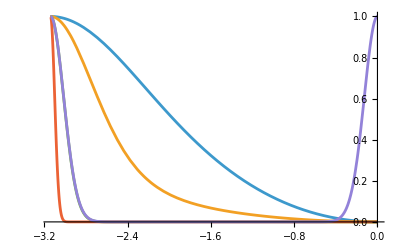

```mathematica
Plot[{pk/.τ->.05,pk/.τ->.5,pk/.τ->5,pk/.τ->50,Exp[-2*Pi*Sin[(k+Pi)]^2*5]},{k,-Pi,0},PlotRange->All]
```

```mathematica
How
```

```mathematica
pk
```

Abs[-ⅈ ⅇ^((3 ⅈ π)/4-1/4 π Conjugate[τ] Conjugate[Sin[k]]^2) Conjugate[√τ ParabolicCylinderD[-1+ⅈ τ Sin[k]^2,-2 ⅇ^((3 ⅈ π)/4) √τ Cos[k]] Sin[k]] Cos[k/2]-ⅇ^(-1/4 π Conjugate[τ] Conjugate[Sin[k]]^2) Conjugate[ParabolicCylinderD[ⅈ τ Sin[k]^2,-2 ⅇ^((3 ⅈ π)/4) √τ Cos[k]]] Sin[k/2]]^2

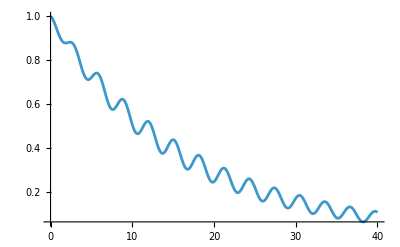

-Graphics-

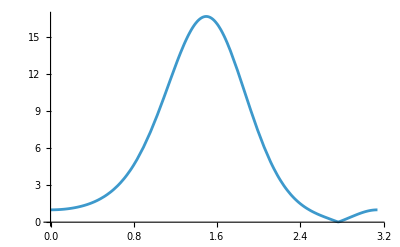

$Aborted

ⅇ^(-1/2 π τ Sin[q]^2) Conjugate[ParabolicCylinderD[ⅈ τ Sin[q]^2,-2 (-1)^(3/4) √τ Cos[q]]] ParabolicCylinderD[ⅈ τ Sin[q]^2,-2 (-1)^(3/4) √τ Cos[q]]

{0.000213884,{q→2.88543}}

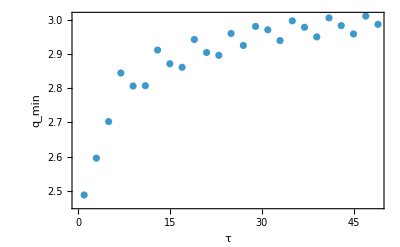

```mathematica
taus=Range[1,100,4];

mins=Table[{τ,q/. Last@NMinimize[{Abs[v[q]]^2/. τ->τ,0<=q<=Pi},q]},{τ,taus}];

ListPlot[mins,Frame->True,FrameLabel->{"τ","q_min"},PlotRange->All]
```

```mathematica
(*Find the k where the excitation probability is exactly 0.5*)q/. FindRoot[(Abs[v[q,tau]]^2)==0.5,{q,1.5} (*Starting guess near Pi/2*)]
```

FindRoot::nlnum: The function value {-0.5+2.71828^(-1.56294 Re[tau]) Abs[ParabolicCylinderD[(0.+0.994996 ⅈ) tau,(0.100038-0.100038 ⅈ) Power[«2»]]]^2} is not a list of numbers with dimensions {1} at {q} = {1.5}.

ReplaceAll::reps: {FindRoot[Abs[v[q,tau]]^2==0.5,{q,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

q/.FindRoot[Abs[v[q,tau]]^2==0.5,{q,1.5}]

```mathematica
findCriticalK[100]
```

```mathematica
ResourceFunction["CriticalPoints"][findCriticalK[100],findCriticalK[100]]
```

[findCriticalK[100],findCriticalK[100]]

```mathematica
qStar
```

2.3044930076218686556032917779333144017167667808628

```mathematica
tauVal=1;

sol=FindRoot[{Re[Gk[q,t,tauVal]]==0,Im[Gk[q,t,tauVal]]==0},{{q,Pi/2+.05,Pi/2-.3,Pi/2+Pi/2},{t,Pi/4,0,Pi/2}},WorkingPrecision->50];

q/. sol
```

2.2291811644121228674511947649306681465321196094026

{q→1.57079632679489661923132169164,t→0.78539816339744830961566084582}

```mathematica
Abs[v[q,τ]]^2==1/2
```

ⅇ^(-1/2 π Re[τ Sin[q]^2]) Abs[ParabolicCylinderD[ⅈ τ Sin[q]^2,-2 ⅇ^((3 ⅈ π)/4) √τ Cos[q]]]^2==1/2

```mathematica
tauVal=3;

FindRoot[Abs[v[q,tauVal]]^2-1/2==0,{q,1/Sqrt[2*Pi*tauVal],-Pi,Pi},WorkingPrecision->10]
```

{q→1.570811377}

```mathematica
taus=Range[0,1,.02];
qsol=ConstantArray[0.,Length[taus]];
qsol[[1]]=Pi/2;

Do[qsol[[i]]=q/. FindRoot[Abs[u[q,taus[[i]]]]^2-1/2==0,{q,qsol[[i-1]],Pi/2-.4,Pi/2+.4},WorkingPrecision->40],{i,2,Length[taus]}]
```

FindRoot::precw: The precision of the argument function (-1/2+0.02 ⅇ^(-0.0314159 Re[Sin[«1»]^2]) Abs[ParabolicCylinderD[Plus[«2»],Times[«2»]] Sin[q]]^2==0) is less than WorkingPrecision (40.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (-1/2+0.04 ⅇ^(-0.0628319 Re[Sin[«1»]^2]) Abs[ParabolicCylinderD[Plus[«2»],Times[«2»]] Sin[q]]^2==0) is less than WorkingPrecision (40.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (-1/2+0.06 ⅇ^(-0.0942478 Re[Sin[«1»]^2]) Abs[ParabolicCylinderD[Plus[«2»],Times[«2»]] Sin[q]]^2==0) is less than WorkingPrecision (40.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {1.970796326794896469181139764259569346905} is at the edge of the search region {1.170796326794896646816823704284615814686,1.970796326794896469181139764259569346905} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

1.+2.80053×10^-18 ⅈ

1.+0. ⅈ

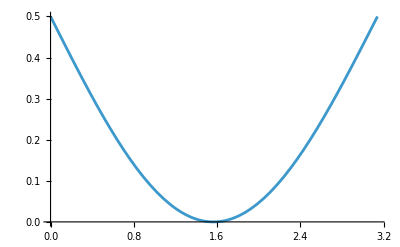

```mathematica
(*---definitions you already have---*)f[a_,b_]:=ParabolicCylinderD[a,b];

B[q_]:=Sin[q];
A[q_]:=1+Cos[q];

ω[q_]:=2*Sqrt[(1-A[q])^2+B[q]^2];

U[q_,t_]:={{Cos[2 t]-I Cos[q] Sin[2 t],Sin[q] Sin[2 t]},{-Sin[q] Sin[2 t],Cos[2 t]+I Cos[q] Sin[2 t]}};

v[q_]:=-Exp[-Pi*B[q]^2*τ/4]*f[I*B[q]^2*τ,Exp[I*3*Pi/4]*2*(1-A[q])*Sqrt[τ]];

u[q_]:=Exp[-I*3*Pi/4] B[q] Sqrt[τ]*Exp[-Pi*B[q]^2*τ/4]*f[I*B[q]^2*τ-1,Exp[I*3*Pi/4]*2*(1-A[q])*Sqrt[τ]];

(*---final Hamiltonian eigenbasis angle at g_f=0---*)

theta[q_]:=ArcTan[B[q],1-A[q]];

(*---excited-state coefficient b_k---*)

bk[q_]:=Cos[theta[q]/2]*u[q]+Sin[theta[q]/2]*v[q];

(*---excitation probability---*)

x=Abs[bk[q]]^2;
Plot[x/.τ->0.00001,{q,0,Pi}]
```

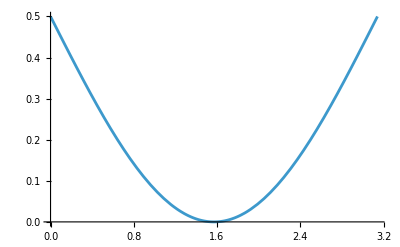

```mathematica
x=Abs[bk[q]]^2;

Plot[x/.τ->0,{q,0,Pi}]
```

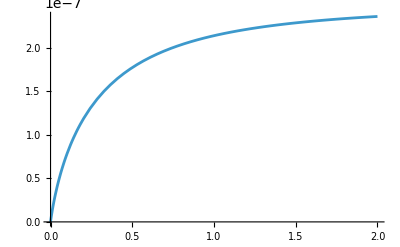

```mathematica
Plot[u[q]*Conjugate[u[q]]/.q->.001,{τ,0,2}]
```

```mathematica
ClearAll["Global`*"]

(*definitions*)
f[a_,b_]:=ParabolicCylinderD[a,b];

B[q_]:=Sin[q];
A[q_]:=1+Cos[q];

ω[q_]:=2*Sqrt[(1-A[q])^2+B[q]^2];

(*time–dependent arguments*)
z[q_,t_,τ_]:=Exp[I*3*Pi/4]*2*(t-A[q]*τ)/Sqrt[τ];

(*u_q(t)*)
u[q_,t_,τ_]:=Exp[-I*3*Pi/4]*B[q]*Sqrt[τ]*Exp[-Pi*B[q]^2*τ/4]*f[I*B[q]^2*τ-1,z[q,t,τ]];

(*v_q(t)*)
v[q_,t_,τ_]:=-Exp[-Pi*B[q]^2*τ/4]*f[I*B[q]^2*τ,z[q,t,τ]];
```

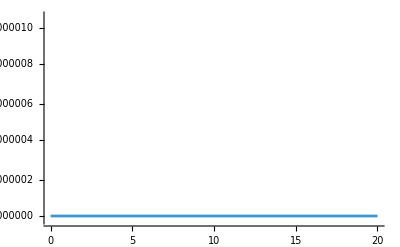

```mathematica
Plot[{Abs[v[q,τ,τ] *Conjugate[v[q,τ,τ]]]}/.q->Pi/.1,{τ,0.001,20}]
```